# Figure 4 and 5

```mathematica
SetDirectory[NotebookDirectory[]];
```

All data were generated with julia code https://github.com/djuliannader/RabiModel.git

#### Fig 5 (a)

```mathematica
Datratio={{1.43765,2.66177159095521/(3*(0.7854369860954992)^2)},{1.4378,1.5169870351760373/(3*(0.7055359738093709)^2)},{1.438,1.4815913320515022/(3*(0.7029937120145018)^2)},{1.44,1.4757657373545028/(3*(0.702558789994917)^2)},{1.8,1.4804338466759013/(3*(0.7038598546251793)^2)},{2,1.4826711454116026/(3*(0.7048231760836707)^2)},{2.16,1.4490049071265219/(3*(0.7061406749154278)^2)},{2.17,1.3863853655159344/(3*(0.7153061207129595)^2)},{2.171,1.4168767416608778/(3*(0.7286635033147801)^2)},{2.172,1.9377147439800826/(3*(0.81222047059144)^2)},{2.173,16.29632763916514/(3*(1.9369682005842725)^2)},{2.174,2.5951275360607524/(3*(0.7651416647091837)^2)},{2.175,1.9414680895647694/(3*(0.72365039016123781)^2)},{2.176,1.7611649433521692/(3*(0.7143596816245358)^2)},{2.177,1.6810601458765666/(3*(0.7108613296386054)^2)},{2.178,1.6366659117420055/(3*(0.709175125110326)^2)},{2.179,1.608712629685433/(3*(0.70823471952626)^2)},{2.18,1.5895896552123816/(3*(0.707657233852783)^2)},{2.19,1.528163567649918/(3*(0.7063076172528544)^2)},{2.2,1.5140183889095455/(3*(0.7061783725725455)^2)},{2.3,1.4987140367214995/(3*(0.7067305556534574)^2)},{2.4,1.4999086428290715/(3*(0.707501450440499)^2)},{2.6,1.5065139051300453/(3*(0.7093556742239)^2)},{2.8,1.5161487996567153/(3*(0.7117376874821352)^2)},{3,1.5292345174415145/(3*(0.7148736811345155)^2)},{3.2,1.5473378581929043/(3*(0.7191500007482132)^2)},{3.4,1.5735669714806557/(3*(0.7252774714763635)^2)},{3.6,1.6144953886255133/(3*(0.7347202949090073)^2)},{3.8,1.6866178199689612/(3*(0.7510542354472962)^2)},{4,1.8463251475360218/(3*(0.7859501826061289)^2)},{4.05,1.921930129865131/(3*(0.8018924424079559)^2)},{4.1,2.0306044987311065/(3*(0.824190700970982)^2)},{4.15,2.2007587218039806/(3*(0.857703849099043)^2)},{4.2,2.509582248375656/(3*(0.9143650905013767)^2)},{4.21,2.627878483040758/(3*(0.9318022666584074)^2)},{4.22,2.723101271334619/(3*(0.9503968037003022)^2)},{4.23,2.8944245388982073/(3*(0.9747821778208932)^2)},{4.24,3.0583462116812927/(3*(1.0023352619908075)^2)},{4.25,3.389205445032044/(3*(1.0427141236615913)^2)},{4.26,3.6455320791573445/(3*(1.08514697318246)^2)},{4.27,4.263144412905323/(3*(1.1589516001374705)^2)},{4.28,9.106777600412286/(3*(1.5379973802228004)^2)},{4.29,5.009305116323149/(3*(1.298401027669174)^2)},{4.3,7.225584732347192/(3*(1.5657773457166166)^2)},{4.31,23.51047646811368/(3*(3.1739957150406455)^2)},{4.32,6.667595376802441/(3*(1.5403661790288146)^2)},{4.33,6.378456792198849/(3*(1.6986147774986553)^2)},{4.34,11.238669257615486/(3*(2.4547048136108063)^2)},{4.35,9.285948647973168/(3*(1.9161226150931423)^2)},{4.36,3.512592777971559/(3*(1.2003200155574583)^2)},{4.37,2.6675184410959742/(3*(1.2170032894196336)^2)},{4.38,3.3189856631886965/(3*(1.4521908723485146)^2)},{4.39,4.556518693535752/(3*(1.7771418513947501)^2)},{4.4,1.3624364588667235/(3*(0.45358134657721205)^2)},{4.45,0.31804071499508635/(3*(0.3307398933663926)^2)},{4.5,0.5781372417233215/(3*(0.444970851723112)^2)},{4.55,0.7627866595933167/(3*(0.5073100003557008)^2)},{4.6,0.8836264103860543/(3*(0.5445846243696765)^2)},{4.65,0.9673876865078146/(3*(0.5691835682981194)^2)},{4.7,1.0285712112683008/(3*(0.5865941751802651)^2)},{4.75,1.0751336341093418/(3*(0.5995540966836929)^2)},{4.8,1.1117218521651822/(3*(0.6095716784669256)^2)},{4.85,1.141213376564446/(3*(0.6175440847287642)^2)},{4.9,1.165479998584639/(3*(0.62403777061109334)^2)},{4.95,1.1857900748055918/(3*(0.6294278340949261)^2)},{5,1.203032871202988/(3*(0.6339724187347134)^2)},{5.1,1.2307161074934383/(3*(0.6412095625125688)^2)},{5.2,1.2519456111035943/(3*(0.646711152203649)^2)},{5.4,1.282303311233143/(3*(0.6545071938969372)^2)},{5.6,1.3028908341150829/(3*(0.6597478045163958)^2)},{5.8,1.3176954398174354/(3*(0.6634939639060021)^2)},{6,1.3287841177848712/(3*(0.6662883359546614)^2)},{6.2,1.3373284849452312/(3*(0.668436462836212)^2)},{6.4,1.344008201226458/(3*(0.6701224488289622)^2)},{6.6,1.3495817651792015/(3*(0.671462718037129)^2)},{6.8,1.3537772781688207/(3*(0.6725319817099877)^2)},{7,1.357159049312992/(3*(0.6733785352303069)^2)},{7.2,1.3597701945404914/(3*(0.6740302369491964)^2)},{7.4,1.361642548573328/(3*(0.6744970061802391)^2)},{7.6,1.362728724525721/(3*(0.674767798375232)^2)},{7.8,1.362850635859937/(3*(0.6747987014587183)^2)},{8,1.3615603661028028/(3*(0.6744783994993284)^2)},{8.2,1.3576970584225454/(3*(0.6735172549155746)^2)},{8.4,1.3474995077888143/(3*(0.6709716392627754)^2)},{8.6,1.309590838785831/(3*(0.6613714408733862)^2)},{8.65,1.2803954285879144/(3*(0.6536845339792502)^2)},{8.7,1.1900318303062452/(3*(0.6359376639835618)^2)},{8.75,0.7846978102188293/(3*(0.5208710571755282)^2)},{8.76,0.5375415287314146/(3*(0.3966211991248306)^2)},{8.768,9.497922092982098/(3*(2.2794644445742347)^2)},{8.77,6.101540958233601/(3*(1.6564279738468262)^2)},{8.78,2.5116437838860572/(3*(0.9368252088903658)^2)},{8.79,1.9905822106458892(3*(0.821985227293116)^2)},{8.8,1.7959198248942703/(3*(0.7776798939976056)^2)},{8.85,1.5411024305093008/(3*(0.7180700255634173)^2)},{8.9,1.4812743936843282/(3*(0.70373370850232)^2)},{9,1.4399069639206517/(3*(0.6937233316052716)^2)},{9.2,1.4156296056331563/(3*(0.687805456898295)^2)},{9.4,1.4073809547613132/(3*(0.6857867214004112)^2)},{9.6,1.403517261516781/(3*(0.6848397162380693)^2)},{10.2,1.3995815527434015/(3*0.6838743663306115^2)}};
DatratioSigx={{1.2,1.4641642416988403/(3*0.6996676385780949^2)},{1.3,1.466448498969988/(3*0.7002235674836149^2)},{1.4,1.4642214246456215/(3*0.6996816171592488^2)},{1.5,1.4642513350916895/(3*0.6996889016948548^2)},{1.6,1.4642826330024208/(3*0.6996965262830501^2)},{1.7,1.464330358693038/(3*0.6997063114046829^2)},{1.72,1.4645206619585747/(3*0.6997248724421308^2)},{1.73,1.8853046732651018/(3*0.734008288001937^2)},{1.74,1.4645888261441056/(3*0.6997259103531756^2)},{1.8,1.46436464641072/(3*0.6997131857693675^2)},{1.9,1.4643965514268191/(3*0.6997216751522023^2)},{2,1.464438376537456/(3*0.6997310804837965^2)},{2.1,1.4644866703617592/(3*0.6997413022720269^2)},{2.2,1.4645437525763738/(3*0.6997526250018166^2)},{2.3,1.4646150105861755/(3*0.6997656427736136^2)},{2.4,1.464712151168507/(3*0.6997816473071045^2)},{2.5,1.4648637072367092/(3*0.6998038301409408^2)},{2.6,1.4651538095523933/(3*0.6998417530866776^2)},{2.7,1.4659232788337282/(3*0.6999347727072308^2)},{2.8,1.4698574727945883/(3*0.7003972229362107^2)},{2.82,1.4732420786619378/(3*0.7007522737623529^2)},{2.84,1.4791193295680667/(3*0.7014555540171146^2)},{2.86,1.4982535755328943/(3*0.7035607241410561^2)},{2.88,1.5784031093653017/(3*0.7117073860281857^2)},{2.9,2.7930066415711234/(3*0.8586712235836926^2)},{2.91,4.888888335317017/(3*1.1133313097843065^2)},{2.92,1.7928610208249247/(3*0.7397229002869303^2)},{2.94,1.5206846576832735/(3*0.7067042569534958^2)},{2.96,1.4871892157113504/(3*0.7026144585747781^2)},{2.98,1.4768879068011425/(3*0.701350656120807^2)},{3,1.472409683215701/(3*0.7007992459391457^2)},{3.1,1.466782142445643/(3*0.7001044547945368^2)},{3.2,1.465809702803749/(3*0.6999874997191695^2)},{3.4,1.465496242421936/(3*0.6999539877583566^2)},{3.4,1.4653730573906216/(3*0.6999451623795275^2)},{3.5,1.4653249054160928/(3*0.6999464509751131^2)},{3.6,1.465311518212925/(3*0.6999527725013718^2)},{3.7,1.4653149726466177/(3*0.6999619485690182^2)},{3.8,1.4653250699645066/(3*0.699972898963089^2)},{3.9,1.4653334182990283/(3*0.6999850211581699^2)},{4,1.4653288156908246/(3*0.6999979371388515^2)},{4.1,1.4652868047814718/(3*0.700011364308641^2)},{4.2,1.4651194764916038/(3*0.7000249744270852^2)},{4.3,1.4639237197442865/(3*0.70003736057494^2)},{4.4,1.4670798391859394/(3*0.7000579312759242^2)},{4.5,1.466297140944912/(3*0.7000703755825161^2)},{4.6,1.466165822595685/(3*0.7000844517375249^2)},{4.7,1.4661388252529353/(3*0.7000986354644533^2)},{4.8,1.4661470524408586/(3*0.7001126655862068^2)},{4.9,1.4661706561513435/(3*0.7001263938957554^2)},{5,1.4662015697581874/(3*0.7001396939277109^2)},{5.1,1.4662357009771714/(3*0.7001524422110673^2)},{5.2,1.466271812261286/(3*0.7001645209712083^2)},{5.3,1.466305109291249/(3*0.7001757800710484^2)},{5.4,1.466337301428369/(3*0.700186108041026^2)},{5.5,1.4663665575628912/(3*0.7001953680134778^2)},{5.6,1.4663920754113253/(3*0.7002034344717428^2)},{5.7,1.46641322524412/(3*0.700210195400294^2)},{5.8,1.46642956183519/(3*0.7002155643430414^2)},{5.9,1.4664408788008891/(3*0.7002194984772292^2)},{6,1.4664473162584568/(3*0.7002220252883695^2)},{6.1,1.4664495181919257/(3*0.7002232817900061^2)},{6.2,1.4664488752530047/(3*0.7002235721150207^2)},{6.3,1.4664478834737247/(3*0.7002234522756643^2)},{6.4,1.466450676078119/(3*0.700223855451847^2)},{6.5,1.4664638148338305/(3*0.7002262783824688^2)},{6.6,1.4664974763866507/(3*0.7002330610067953^2)},{6.7,1.4665672488865287/(3*0.7002478104194323^2)},{6.8,1.466696887559632/(3*0.7002760517866096^2)},{6.9,1.4669226061417282/(3*0.7003262428844825^2)},{7,1.4672998830551345/(3*0.7004113838674928^2)},{7.1,1.4679144925798178/(3*0.7005516261621314^2)},{7.2,1.4689008539335784/(3*0.7007786088430437^2)},{7.3,1.4704735266113054/(3*0.7011428893594194^2)},{7.4,1.4729833965929382/(3*0.7017271602041799^2)},{7.5,1.4770228727366121/(3*0.7026708750563908^2)},{7.6,1.4836354665633866/(3*0.7042189430033077^2)},{7.7,1.4947692576712541/(3*0.706825876599313^2)},{7.8,1.5143772980746797/(3*0.7114040460292523^2)},{7.9,1.5515836747076683/(3*0.7200178391909846^2)},{8,1.6327837762486297/(3*0.7384067815019262^2)},{8.1,1.8974480783200747/(3*0.7922047512236317^2)},{8.2,412.7512884267949/(3*4.65578574482814^2)},{8.3,885.305061183595/(3*13.78359504205587^2)},{8.4,0.253200594848181/(3*0.288691113530259^2)},{8.5,0.2943836945006524/(3*0.312942105559042^2)},{8.6,0.3432535913298125/(3*0.33936888086340744^2)},{8.7,0.4008674409162154/(3*0.3678702355066452^2)},{8.8,0.46780702069222/(3*0.39810039792835994^2)},{8.9,0.5437049220636396/(3*0.42940560835534747^2)},{9,0.6267997160032905/(3*0.46083023213481056^2)},{9.1,0.7138470453056911/(3*0.491239638281205^2)},{9.2,0.8006639697595901/(3*0.5195476844261231^2)},{9.4,0.9583117749247592/(3*0.5670532180643875^2)},{9.6,1.0815062012211687/(3*0.6015654612853596^2)},{9.8,1.1704512761421126/(3*0.6254079641186427^2)},{10,1.2331176781802928/(3*0.6417613012284544^2)},{10.2,1.2775191384337523/(3*0.6531536635852435^2)}};
```

```mathematica
Dataratio=Table[{Datratio[[i,1]]/(8.801011),Datratio[[i,2]]},{i,1,Length[Datratio]}];
DataratioSigx=Table[{DatratioSigx[[i,1]]/(8.801011),DatratioSigx[[i,2]]},{i,1,Length[DatratioSigx]}];
```

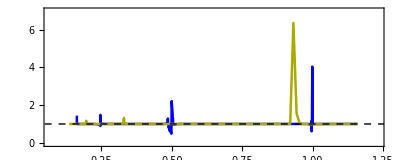

```mathematica
fig4a=Show[ListPlot[{Dataratio,DataratioSigx},Joined->True,
PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{-0.05,7}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0,1.5},PlotStyle->{Dashed,Black,Thick}],AspectRatio->0.4]
```

```mathematica
Export["Ratio.png",fig4a];
```

#### Fig 5 (b)

```mathematica
Datratiop={{1.43765,0.7482511728317965/(3*(0.4062433543824589)^2)},{1.4378,0.399509042325154/(3*(0.36181873676264803)^2)},{1.438,0.38941105865418335/(3*(0.360410502676795)^2)},{1.44,0.3879331481268071/(3*(0.3601649754564568)^2)},{1.8,0.3863439608086134/(3*(0.3595010087652746)^2)},{2,0.38485584727638233/(3*(0.3590219076461521)^2)},{2.16,0.37495289684120436/(3*(0.35895524795381917)^2)},{2.17,0.36358130192578403/(3*(0.36453855700244975)^2)},{2.171,0.37657985079177947/(3*(0.37220263942939896)^2)},{2.172,0.5375628643831135/(3*(0.4186496102620877)^2)},{2.173,4.4762531973568915/(3*(1.0098627609201427)^2)},{2.174,0.6760709622424088/(3*(0.38805087701527224)^2)},{2.175,0.5008690156998623/(3*(0.36681153323704374)^2)},{2.176,0.4534415986905414/(3*(0.3622052329645297)^2)},{2.177,0.4326290844137216/(3*(0.3605239130665569)^2)},{2.178,0.4211945996897211/(3*(0.3597367868640341)^2)},{2.179,(3*(0.3593095750989857)^2)},{2.18,0.4091685720835601/(3*(0.3590536508771601)^2)},{2.19,0.39362314220834005/(3*(0.3584799982335484)^2)},{2.2,0.3899926853443754/(3*(0.3584000101878287)^2)},{2.3,0.3847820323811013/(3*(0.3580505532564072)^2)},{2.4,0.3834375034010616/(3*(0.35766591244948853)^2)},{2.6,0.3811507524647495/(3*(0.35674381599079147)^2)},{2.8,0.3785152833282498/(3*(0.3555651734137215)^2)},{3,0.3751714680673069/(3*(0.3540249007639039)^2)},{3.2,0.3707216538366244/(3*(0.3519458963099424)^2)},{3.4,0.3645064770092295/(3*(0.3490094608893358)^2)},{3.6,0.3552487254355047/(3*(0.34457997301774934)^2)},{3.8,0.3400703401219882/(3*(0.33718073501845)^2)},{4,0.3108152511905364/(3*(0.32240245766761677)^2)},{4.05,0.2987374198575882/(3*(0.3160784331206613)^2)},{4.1,0.28305156124558434/(3*(0.30764271355978284)^2)},{4.15,0.26185777507213953/(3*(0.29578755790932293)^2)},{4.2,0.23161438566719428/(3*(0.2777207679011433)^2)},{4.21,0.23606459469982038/(3*(0.2735268035224528)^2)},{4.22,0.21564683004782828/(3*(0.2673718145355726)^2)},{4.23,0.21214176824151135/(3*(0.2613134500374244)^2)},{4.24,0.19857669930568303/(3*(0.25399166649321187)^2)},{4.25,0.19839325461642707/(3*(0.2455627847527906)^2)},{4.26,0.30783551959002386/(3*(0.24711686221111476)^2)},{4.27,0.22319273168085513/(3*(0.22658862125863763)^2)},{4.28,1.3798624943684032/(3*(0.28707251768236386)^2)},{4.29,0.9958432477724488/(3*(0.28548305963963877)^2)},{4.3,0.9148999621429108/(3*(0.24554188119770323)^2)},{4.31,6.853151860730768/(3*(0.7683505986301614)^2)},{4.32,5.401199142944598/(3*(0.8254869678274537)^2)},{4.33,2.98106475011136/(3*(0.5126987869196142)^2)},{4.34,4.945432931138579/(3*(0.7318370288368984)^2)},{4.35,13.833242879246054/(3*(2.337601775128362)^2)},{4.36,3.512592777971559/(3*(1.3351488655432675)^2)},{4.37,4.779801041061898/(3*(0.9844570276896767)^2)},{4.38,4.6330242724922845/(3*(0.9677714299324532)^2)},{4.39,5.517684215092675/(3*(1.1561468997426074)^2)},{4.4,7.23024030724348/(3*(2.072323873510602)^2)},{4.45,1.6374956881039546/(3*(0.778786114091589)^2)},{4.5,0.9371301360625817/(3*(0.5669018542692883)^2)},{4.55,0.7328331356793495/(3*(0.49720403765829074)^2)},{4.6,0.6399644299485827/(3*(0.46339649773143965)^2)},{4.65,0.587590447301273/(3*(0.44354062514229936)^2)},{4.7,0.5541346556365275/(3*(0.43049959342062766)^2)},{4.75,0.5309700309291392/(3*(0.421285691217679)^2)},{4.8,0.514003620515355/(3*(0.41443272314805607)^2)},{4.85,0.5010522113118796/(3*(0.4091379793402944)^2)},{4.9,0.49084755751978953/(3*(0.4049253930345933)^2)},{4.95,0.48260352361441206/(3*(0.4014948345619453)^2)},{5,0.47580729671103206/(3*(0.39864774663165353)^2)},{5.1,0.4652673658770568/(3*(0.39419718267669146)^2)},{5.2,0.4574802119305985/(3*(0.3908805887992634)^2)},{5.4,0.44676597008233326/(3*(0.386276306926167)^2)},{5.6,0.43976761029988604/(3*(0.3832423959300918)^2)},{5.8,0.43486196146311595/(3*(0.38110301477594455)^2)},{6,0.4312534600152699/(3*(0.37952283290616634)^2)},{6.2,0.42850656574110474/(3*(0.3783170657066284)^2)},{6.4,0.42635511260731546/(3*(0.37737617716918387)^2)},{6.6,0.4247326473382143/(3*(0.3766310736454861)^2)},{6.8,0.4233667555069774/(3*(0.37603922594526756)^2)},{7,0.4223066218006351/(3*(0.37557184752184486)^2)},{7.2,0.42149460710608416/(3*(0.3752128004719081)^2)},{7.4,0.420914556579401/(3*(0.37495602072695067)^2)},{7.6,0.4205782600579702/(3*(0.37480715132490006)^2)},{7.8,0.4205389875346018/(3*(0.374790038174301)^2)},{8,1.3615603661028028/(3*(0.6744783994993284)^2)},{8.2,0.4221263573708255/(3*(0.37549452584569887)^2)},{8.4,0.42531114891789984/(3*(0.3769024319585569)^2)},{8.6,0.4377210923943334/(3*(0.3823096054238859)^2)},{8.65,0.44831902724463424/(3*(0.38675276751794097)^2)},{8.7,0.46547949151823653/(3*(0.3976674192258115)^2)},{8.75,0.6790608390431903/(3*(0.48580760722727573)^2)},{8.76,1.1887912415772992/(3*(0.6853097180454782)^2)},{8.768,0.6662618451061901/(3*(0.2982544094197565)^2)},{8.77,0.2434809252666748/(3*(0.20817334313748107)^2)},{8.78,0.21419516992619983/(3*(0.2722340685154405)^2)},{8.79,0.28098341530338683/(3*(0.3086092558009889)^2)},{8.8,0.3154746917484532/(3*(0.3258282034653259)^2)},{8.85,0.37145131363468437/(3*(0.3524692487176215)^2)},{8.9,0.38681784526207214/(3*(0.3595589079882065)^2)},{9,0.3980477354950827/(3*(0.36468380435583164)^2)},{9.2,0.40489311178968584/(3*(0.36778375991549966)^2)},{9.4,0.4072647831750278/(3*(0.3688533737211679)^2)},{9.6,0.4083836740690294/(3*(0.36935721189306975)^2)},{10.2,0.409527387754794/(3*0.36987184430403436^2)}};
DatratiopSigx={{1.2,0.3921628869726618/(3*0.36203050980355783^2)},{1.3,0.3921559998579701/(3*0.3620273477329027^2)},{1.4,0.39214913506400656/(3*0.3620241415962837^2)},{1.5,0.39214230441869724/(3*0.3620208693197166^2)},{1.6,0.392135893008764/(3*0.3620175458506972^2)},{1.7,0.3921398959601713/(3*0.36201521304407863^2)},{1.72,0.3922116059957017/(3*0.362024085682631^2)},{1.73,0.5160488344127852/(3*0.38091948076058246^2)},{1.74,0.392173857030967/(3*0.3620223661092071^2)},{1.8,0.3921191382461764/(3*0.3620107245705201^2)},{1.9,0.3921122980596464/(3*0.3620070127745121^2)},{2,0.3921060320236967/(3*0.3620034815088899^2)},{2.1,0.3921007000854459/(3*0.36200010762598495^2)},{2.2,0.3920972428083919/(3*0.36199708189135016^2)},{2.3,0.39209740918916103/(3*0.3619947904836448^2)},{2.4,0.3921048499769309/(3*0.36199405166474286^2)},{2.5,0.3921283049576889/(3*0.3619968299603092^2)},{2.6,0.3921931812467198/(3*0.3620088397421654^2)},{2.7,0.3924010755811677/(3*0.3620529194990843^2)},{2.8,0.39354354282888243/(3*0.36230605362785906^2)},{2.82,0.394557901243948/(3*0.36250358317381653^2)},{2.84,0.39628585042452724/(3*0.36289200290498386^2)},{2.86,0.4019748234663812/(3*0.36405149842167067^2)},{2.88,0.42455651763250196/(3*0.36850598013364255^2)},{2.9,0.7704876156015832/(3*0.4477343585216411^2)},{2.91,1.3645528531995557/(3*0.5830564022323315^2)},{2.92,0.48488635644255257/(3*0.3830971350540989^2)},{2.94,0.40768680043369915/(3*0.3655298076585982^2)},{2.96,0.3982159715774305/(3*0.36337274096001865^2)},{2.98,0.3953103689450141/(3*0.36271041671436727^2)},{3,0.3940489211822413/(3*0.36242250880471305^2)},{3.1,0.3924558736050032/(3*0.3620566685085751^2)},{3.2,0.3921622623088867/(3*0.36198684825041044^2)},{3.3,0.39204929991429016/(3*0.3619582091253861^2)},{3.4,0.39198734223119797/(3*0.3619412249987856^2)},{3.5,0.3919448934771103/(3*0.3619287453546111^2)},{3.6,0.39191110298011744/(3*0.36191834314623594^2)},{3.7,0.39188123374154915/(3*0.3619090156343779^2)},{3.8,0.39185266841697497/(3*0.3619002956712767^2)},{3.9,0.39182331206235543/(3*0.36189195420104553^2)},{4,0.3917904062104909/(3*0.36188389083124^2)},{4.1,0.39174789330555737/(3*0.3618761142494887^2)},{4.2,0.39167383674716294/(3*0.3618688916669992^2)},{4.3,0.39134222264764207/(3*0.36186554931759757^2)},{4.4,0.39210106174252773/(3*0.36184732340472475^2)},{4.5,0.3918728306673337/(3*0.36184223131827503^2)},{4.6,0.3918083467374787/(3*0.3618353074848888^2)},{4.7,0.39177052909380466/(3*0.3618282152825118^2)},{4.8,0.39174222807785936/(3*0.3618212050330231^2)},{4.9,0.3917186614344857/(3*0.3618143784993555^2)},{5,0.3916980189152075/(3*0.36180780510652993^2)},{5.1,0.3916795090131647/(3*0.36180154627124506^2)},{5.2,0.3916627384163725/(3*0.36179565417244913^2)},{5.3,0.3916476383913245/(3*0.3617902102517986^2)},{5.4,0.39163409308039726/(3*0.36178525677979995^2)},{5.5,0.39162214707596427/(3*0.3617808598036041^2)},{5.6,0.3916118556954524/(3*0.36177707642514456^2)},{5.7,0.39160328353567/(3*0.3617739558731227^2)},{5.8,0.39159648425744314/(3*0.36177153309380716^2)},{5.9,0.3915914725339793/(3*0.3617698191355743^2)},{6,0.39158819544542595/(3*0.36176878705957105^2)},{6.1,0.3915864839090582/(3*0.36176835128912954^2)},{6.2,0.39158598832481384/(3*0.36176833741649067^2)},{6.3,0.39158608346160295/(3*0.3617684378980381^2)},{6.4,0.39158572874045666/(3*0.36176814673741337^2)},{6.5,0.3915832609324546/(3*0.3617666625390244^2)},{6.6,0.39157608359812085/(3*0.36176274337183617^2)},{6.7,0.3915601967632102/(3*0.3617544871924691^2)},{6.8,0.3915294756438141/(3*0.36173899544529736^2)},{6.9,0.3914745482038168/(3*0.3617118499764859^2)},{7,0.3913810182467028/(3*0.36166628532764195^2)},{7.1,0.39122659537087173/(3*0.3615918517939876^2)},{7.2,0.390976348186721/(3*0.3614722027084136^2)},{7.3,0.3905746291916453/(3*0.36128132408485564^2)},{7.4,0.3899308630071618/(3*0.36097687936171635^2)},{7.5,0.3888934708911896/(3*0.3604879385012332^2)},{7.6,0.3871994607233929/(3*0.3596910692792694^2)},{7.7,0.3843701494384812/(3*0.35836026495054757^2)},{7.8,0.3794748090963801/(3*0.3560511854645001^2)},{7.9,0.3705198244177154/(3*0.35179199899358454^2)},{8,0.35250545339218653/(3*0.3430390690603011^2)},{8.1,0.3104295617047616/(3*0.31994365596042834^2)},{8.2,79.37723180679372/(3*2.5351137550771257^2)},{8.3,275.1606929631769/(3*10.27445950340775^2)},{8.4,2.4525107294733437/(3*0.9249321160560994^2)},{8.5,2.0354872719681647/(3*0.8418901653374025^2)},{8.6,1.6947419630190579/(3*0.7670976329484095^2)},{8.7,1.4188440548400296/(3*0.7005124996541805^2)},{8.8,1.1977912469140066/(3*0.6421000351080984^2)},{8.9,1.0227350233233066/(3*0.5917609452385112^2)},{9,0.8857746492644286/(3*0.5492461834261405^2)},{9.1,0.779837959742698/(3*0.5140861773798532^2)},{9.2,0.6986562914929242/(3*0.4855728226405771^2)},{9.4,0.589759059893217/(3*0.444841933029682^2)},{9.6,0.5263336106769556/(3*0.4196237678943245^2)},{9.8,0.4883091868280804/(3*0.40391518613728067^2)},{10,0.46449992497025006/(3*0.39383789452363016^2)},{10.2,0.44888134105072913/(3*0.38712194917333453^2)}};
```

```mathematica
Dataratiop=Table[{Datratiop[[i,1]]/(8.801011),Datratiop[[i,2]]},{i,1,Length[Datratiop]}];
DataratiopSigx=Table[{DatratiopSigx[[i,1]]/(8.801011),DatratiopSigx[[i,2]]},{i,1,Length[DatratiopSigx]}];
```

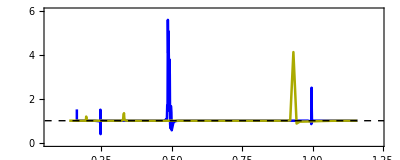

```mathematica
fig4b=Show[ListPlot[{Dataratiop,DataratiopSigx},Joined->True,
PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{-0.05,6}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],AspectRatio->0.4]
```

#### Fig 5 (a)

```mathematica
Datpur={{1.43765,0.9933527494406048},{1.4378,0.9939617883933407},{1.438,0.9939808838571469},{1.44,0.9939840545604032},{1.8,0.9939716172180049},{2,0.9939628093958185},{2.16,0.9939471400229626},{2.17,0.9938576325787606},{2.171,0.9937401732388036},{2.172,0.9930408397555518},{2.173,0.9844498558181207},{2.174,0.9935359901247801},{2.175,0.9938412797130615},{2.176,0.99390607834518},{2.177,0.9939291662423819},{2.178,0.9939396786044137},{2.179,0.993945201000637},{2.18,0.99390483835044198},{2.19,0.9939540332749865},{2.2,0.9939536873642564},{2.3,0.9939469990991234},{2.4,0.993940111581821},{2.6,0.9939240174139341},{2.8,0.9939035440607767},{3,0.9938766919872954},{3.2,0.993840147655041},{3.4,0.9937878454448081},{3.6,0.9937073177262004},{3.8,0.9935681742071859},{4,0.9932715260458058},{4.05,0.9931362969197296},{4.1,0.9929474818586389},{4.15,0.9926644644375624},{4.2,0.9921882805681049},{4.21,0.9920437960183752},{4.22,0.9918872841151444},{4.23,0.9916860044786037},{4.24,0.9914562923249891},{4.25,0.9911277525004414},{4.26,0.9907747802854138},{4.27,0.9901771340084724},{4.28,0.9872672274831625},{4.29,0.9890090490196962},{4.3,0.9868512651202641},{4.31,0.9742478398675603},{4.32,0.9870123734532766},{4.33,0.9855843384293019},{4.34,0.9793780928288868},{4.35,0.9839352331359915},{4.36,0.9897199691181096},{4.37,0.989484168310679},{4.38,0.987451178571527},{4.39,0.9846835119910133},{4.4,0.996211234466161},{4.45,0.997208285274764},{4.5,0.9962057649326731},{4.55,0.9956636810230934},{4.6,0.9953408223417639},{4.65,0.9951282521513838},{4.7,0.9949780380242651},{4.75,0.9948663539247824},{4.8,0.994780104618593},{4.85,0.9947115148954685},{4.9,0.994655682258465},{4.95,0.994609364045394},{5,0.9945703303841835},{5.1,0.9945082103141947},{5.2,0.9944610255985478},{5.4,0.9943942362510872},{5.6,0.9943494100605722},{5.8,0.9943174227791454},{6,0.9942936108538474},{6.2,0.9942753494119471},{6.4,0.9942610540449932},{6.6,0.994249757982159},{6.8,0.9942407595686198},{7,0.9942336844351206},{7.2,0.994228286325874},{7.4,0.9942244791840268},{7.6,0.9942223570653224},{7.8,0.9942222956524223},{8,0.9942252479474886},{8.2,0.9942336943498835},{8.4,0.994255718561624},{8.6,0.9943382299853093},{8.65,0.9944042997740141},{8.7,0.9945543068731445},{8.75,0.9955464930713109},{8.76,0.9966388903783129},{8.768,0.9807528633533986},{8.77,0.9859361939057166},{8.78,0.9919922928281378},{8.79,0.9929676777973113},{8.8,0.9933449135745905},{8.85,0.9938534732468524},{8.9,0.9939760206732551},{9,0.9940617210575275},{9.2,0.9941125827165618},{9.4,0.9941301060289334},{9.6,0.9941384676807977},{10.2,0.9941475418313208}};
DatpurSigx={{1.2,0.9934490543425162},{1.3,0.9934486156332352},{1.4,0.9934482048973593},{1.5,0.993447810008185},{1.6,0.9934474229642255},{1.7,0.9934470304896512},{1.72,0.9934468343807995},{1.73,0.9931566800555539},{1.74,0.9934466931746834},{1.8,0.9934466388014707},{1.9,0.9934462528532261},{2,0.9934458565238665},{2.1,0.9934454533783361},{2.2,0.9934450442795085},{2.3,0.9934446305239149},{2.4,0.9934442135172893},{2.5,0.9934437916485102},{2.6,0.9934433430258719},{2.7,0.9934427055551995},{2.8,0.9934399922238943},{2.82,0.993437678679854},{2.84,0.9934327964381923},{2.86,0.9934170370827485},{2.88,0.9933512237566762},{2.9,0.9920915861741453},{2.91,0.9896939117253647},{2.92,0.9930582109981656},{2.94,0.9933676786144702},{2.96,0.9934082447262026},{2.98,0.993421371269333},{3,0.9934273190583374},{3.1,0.9934351676772973},{3.2,0.9934363673472323},{3.3,0.9934364483880788},{3.4,0.9934361495060134},{3.5,0.9934356707587905},{3.6,0.9934350870013838},{3.7,0.9934344321456422},{3.8,0.9934337236142249},{3.9,0.9934329711050572},{4,0.9934321800242832},{4.1,0.9934313522199238},{4.2,0.9934304814705323},{4.3,0.9934294691609684},{4.4,0.9934289018351301},{4.5,0.9934278968605529},{4.6,0.9934269377752882},{4.7,0.9934259723055958},{4.8,0.9934249962314392},{4.9,0.9934240108231297},{5,0.9934230191306243},{5.1,0.9934220253112853},{5.2,0.9934210347993901},{5.3,0.993420053231645},{5.4,0.9934190888052224},{5.5,0.9934181504535675},{5.6,0.993417249109622},{5.7,0.9934163979001015},{5.8,0.993415612592944},{5.9,0.9934149121494943},{6,0.9934143193986663},{6.1,0.9934138618677845},{6.2,0.9934135728021526},{6.3,0.9934134924197673},{6.4,0.9934136694540496},{6.5,0.9934141630465737},{6.6,0.9934150450573491},{6.7,0.9934164028571943},{6.8,0.9934183426426548},{6.9,0.9934209932419973},{7,0.9934245102049161},{7.1,0.993429079565107},{7.2,0.9934349197584419},{7.3,0.9934422781288955},{7.4,0.9934514136895586},{7.5,0.9934625462214125},{7.6,0.9934757217029117},{7.7,0.9934904583321891},{7.8,0.9935047591675026},{7.9,0.9935119847135347},{8,0.9934882468617019},{8.1,0.9933033334243386},{8.2,0.9723176543441397},{8.3,0.9186768810026241},{8.4,0.9989618064839384},{8.5,0.9987268320805198},{8.6,0.9984556240727782},{8.7,0.9981481640346432},{8.8,0.997807506703015},{8.9,0.9974408121834724},{9,0.9970596131717938},{9.1,0.9966786147232959},{9.2,0.9963129795145117},{9.4,0.9956729349375075},{9.6,0.9951823449469804},{9.8,0.9948263120196976},{10,0.9945709983422354},{10.2,0.9943859215495175}};
```

```mathematica
Dataimp=Table[{Datpur[[i,1]]/(8.801011),1-Datpur[[i,2]]},{i,1,Length[Datpur]}];
DataimpSigx=Table[{DatpurSigx[[i,1]]/(8.801011),1-DatpurSigx[[i,2]]},{i,1,Length[DatpurSigx]}];
```

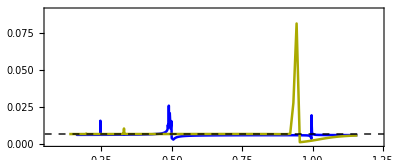

```mathematica
fig4c=Show[ListPlot[{Dataimp,DataimpSigx},Joined->True,PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{0.0,0.09}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{13,Black}],Plot[1-0.9934136182043661,{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],AspectRatio->0.4]
```

```mathematica
Export["Impurities.png",fig4c];
```

#### Fig 5 (b)

```mathematica
Datnn={{1.43765,0.10213964004409326},{1.4378,0.006180404397177375},{1.438,0.0007185854186317897},{1.44,9.813615404496989*10^-5},{1.8,0.0037534943181130043},{2,0.0036342628098346985},{2.16,0.0014794895509175898},{2.17,0.005929708605961537},{2.171,0.01629766138316424},{2.172,0.08141534340153678},{2.173,0.5219203964998027},{2.174,0.042022232243011715},{2.175,0.009925687096497882},{2.176,0.0034962468907218103},{2.177,0.0015269944032589855},{2.178,0.0006667513587870211},{2.179,0.00031689696489678454},{2.18,0.00017432542044582},{2.19,1.2591*10^-5},{2.2,2.516524*10^-5},{2.3,0.003994306117855784},{2.4,0.0038692193124505447},{2.6,0.003728521712607291},{2.8,0.0036380677722100963},{3,0.0035305723949896617},{3.2,0.003403702857674995},{3.4,0.0032329925106564517},{3.6,0.0029887771724737},{3.8,0.002611042726570423},{4,0.0019907103157235095},{4.05,0.0017545368415605722},{4.1,0.0014758260442511162},{4.15,0.001181909944742321},{4.2,8.945691*10^-5},{4.21,0.003123400225836024},{4.22,0.001039707257270761},{4.23,0.007688159169442876},{4.24,0.00497444339962283},{4.25,0.012846634068778284},{4.26,0.05045177417112745},{4.27,0.0346524610682164},{4.28,0.20363517697743472},{4.29,0.15008163422405985},{4.3,0.1558113308797553},{4.31,0.5748690496110065},{4.32,0.43975991527245495},{4.33,0.3119883911000165},{4.34,0.4721643804540283},{4.35,0.7227049848716758},{4.36,0.4681091606950456},{4.37,0.3714889955785583},{4.38,0.39055046302023366},{4.39,0.46268646059985086},{4.4,0.3002622904372383},{4.45,0.007554379743763606},{4.5,0.0004987800772968676},{4.55,0.000159747990006065},{4.6,0.000190843444878519},{4.65,9.726027*10^-5},{4.7,0.00018524700965505403},{4.75,0.00037475208156068085},{4.8,0.0004707097392422366},{4.85,0.0005168751356214862},{4.9,0.0005550700117313845},{4.95,0.0005871766616005747},{5,0.0006145307951188617},{5.1,0.0006448748561624917},{5.2,0.000677354908038108},{5.4,0.000645229037751438},{5.6,0.0006372058093395694},{5.8,0.0006202142452862436},{6,0.0006369563026660252},{6.2,0.0006497895093662276},{6.4,0.0006595137199021384},{6.6,0.000669379878651899},{6.8,0.000675092827463919},{7,0.00068008890510729},{7.2,0.0006839823871827022},{7.4,0.0006867776513899138},{7.6,0.0006883958741890073},{7.8,0.00068856407101614},{8,0.0006866059038055372},{8.2,0.0006807748306121297},{8.4,0.0006654455606480703},{8.6,0.0006103246580499988},{8.65,0.0006116795388300122},{8.7,0.00024625038603198757},{8.75,0.0007065867215267918},{8.76,0.027337669608767712},{8.768,0.22844386271153594},{8.77,0.08581217166627497},{8.78,0.00140630680043774},{8.79,0.0007204460138958702},{8.8,0.0017021458338943862},{8.85,0.0033576011252822724},{8.9,0.0038209695390944987},{9,0.004185613102762886},{9.2,0.004394607558311225},{9.4,0.004467410594464649},{9.6,0.004501826842757239},{10.2,8.024916131610382*10^-7}};
DatnnSigx={{1.2,2*10^(-5)},{1.3,0.003966515599469034},{1.4,0.003965817376120784},{1.5,0.003964924087231481},{1.6,0.003963364090642907},{1.7,0.003909606028812407},{1.72,0.003925244876849421},{1.73,0.03944507160561361},{1.74,0.003977897697708066},{1.8,0.00396639486464978},{1.9,0.003963454432205138},{2,0.0039613671201674805},{2.1,0.003958830345039965},{2.2,0.003956612249071068},{2.3,0.0039525646657998514},{2.4,0.003946825536048859},{2.5,0.0039375704225455},{2.6,0.00391898322629336},{2.7,0.003875382034446151},{2.8,0.0037057069063866077},{2.82,0.0008567825363094972},{2.84,0.00011809784291183512},{2.86,0.00014667449721383896},{2.88,0.010065643177876726},{2.9,0.0878527403842233},{2.91,0.18250605433669698},{2.92,0.007654153308507716},{2.94,0.0035964184261123577},{2.96,0.003776618228757078},{2.98,0.0038619109764730375},{3,0.0039027034318037668},{3.1,0.0039518982517277035},{3.2,0.003955460981474035},{3.3,0.003953657967800783},{3.4,0.003950756922670884},{3.5,0.003947491125735558},{3.6,0.00394397132661739},{3.7,0.003940057725303481},{3.8,0.003935762137799781},{3.9,0.003930694186676353},{4,0.0039243962061221715},{4.1,0.003915663498299526},{4.2,0.0039000886012465763},{4.3,0.0038308978958370155},{4.4,0.0039822686020554166},{4.5,0.003933935453179549},{4.6,0.003917483401714605},{4.7,0.0039054349782274844},{4.8,0.0038942298546025267},{4.9,0.0038827655056430377},{5,0.0038705186154008864},{5.1,0.0038571794168185125},{5.2,0.003840498811015003},{5.3,0.003825466420053214},{5.4,0.0038069341803266266},{5.5,0.003786020078317076},{5.6,0.0037623859943016758},{5.7,0.0037367102563625743},{5.8,0.003710042857482776},{5.9,0.003675125752587549},{6,0.00363531173496745},{6.1,0.0035873726629809255},{6.2,0.003535406363292859},{6.3,0.0034757174149229186},{6.4,0.0034333820884930866},{6.5,0.003361737918070151},{6.6,0.003245391556755406},{6.7,0.003152863589660937},{6.8,0.0030307608693009858},{6.9,0.0028876097459114014},{7,0.0027200769939919045},{7.1,0.0025223765523492148},{7.2,0.002290841446011882},{7.3,0.0020196225167994353},{7.4,0.0017071246952631292},{7.5,0.0013402291646544828},{7.6,0.0009199576918721419},{7.7,0.000445723234276052},{7.8,7*10^(-6)},{7.9,0.00048774302836385175},{8,0.0004557819256876261},{8.1,0.003406471676911549},{8.2,0.9673614372389265},{8.3,2.192149433609411},{8.4,0.011402925723104973},{8.5,0.004978853303621911},{8.6,0.0018528764058474145},{8.7,0.00016324324110272848},{8.8,0.0010662009875987977},{8.9,3.500634423936333^-5},{9,0.008419403993106922},{9.1,0.003602302195180096},{9.2,0.0019272556768779037},{9.4,0.011053170701234238},{9.6,9.410953894350982*10^-5},{9.8,1.6931583283641416*10^-5},{10,1.8246867544924328*10^-5},{10,3.766101601598848*10^-5}};
```

```mathematica
Dataneg=Table[{Datnn[[i,1]]/(8.801011),Datnn[[i,2]]},{i,1,Length[Datnn]}];
DatanegSigx=Table[{DatnnSigx[[i,1]]/(8.801011),DatnnSigx[[i,2]]},{i,1,Length[DatnnSigx]}];
```

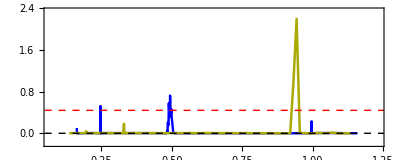

```mathematica
fig4d=Show[ListPlot[{Dataneg,DatanegSigx},Joined->True,PlotStyle->{{Blue,Thickness[0.0043]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{-0.2,2.35}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{13,Black}],Plot[00,{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],Plot[0.44,{x,0.0,1.5},PlotStyle->{Dashed,Red,Thick}],AspectRatio->0.4]
```

#### Fig 5 (c)

```mathematica
Datfisdis={{1.43765,1.5502085500120806},{1.4378,1.3941353854341512},{1.438,1.389162499839122},{1.44,1.3883114118212108},{1.8,1.3908477203292815},{2,1.3927265528529675},{2.16,1.3952822873245212},{2.17,1.4131290983397538},{2.171,1.4391761651152788},{2.172,1.6019800972828946},{2.173,3.7565943374805384},{2.174,1.5107139252854709},{2.175,1.382118818569585},{2.176,1.4114340867229573},{2.177,1.4045804974139933},{2.178,1.401274557468325},{2.179,1.3994294912807075},{2.18,1.3982956742582475},{2.19,1.3956391813180653},{2.2,1.395381488819788},{2.3,1.3964521508545817},{2.4,1.3979559214073416},{2.6,1.4015744437871198},{2.8,1.4062232833620614},{3,1.4123433609488099},{3.2,1.4206880065747003},{3.4,1.432642963337933},{3.6,1.4510616047971816},{3.8,1.4829080278869753},{4,1.5508871314634258},{4.05,1.5819174063318848},{4.1,1.625291857104569},{4.15,1.6904221231357395},{4.2,1.8003791686550765},{4.21,1.8341851550960278},{4.22,1.870200470070952},{4.23,1.917417827891255},{4.24,1.970709807239547},{4.25,2.0487636776085454},{4.26,2.1306308047816804},{4.27,2.2728421746459126},{4.28,2.9990399138063557},{4.29,2.5403291378531443},{4.3,3.050244418924804},{4.31,6.026694727495723},{4.32,3.001640639391336},{4.33,3.3001424426662274},{4.34,4.708759485131133},{4.35,3.710660018429782},{4.36,2.3516525848573506},{4.37,2.3830383066689054},{4.38,2.8317628696796415},{4.39,3.445794397438575},{4.4,0.9003694991684559},{4.45,0.6577962886547093},{4.5,0.8832128480392878},{4.55,1.0058577384950145},{4.6,1.0790663748486593},{4.65,1.1273286246210836},{4.7,1.1614632305245},{4.75,1.1868589001667298},{4.8,1.206481263970348},{4.85,1.2220928101527055},{4.9,1.2348056418400977},{4.95,1.24535576089102},{5,1.2542495294335918},{5.1,1.2684098623599198},{5.2,1.2791721052682783},{5.4,1.29441945831698},{5.6,1.30466682598768},{5.8,1.311990991367831},{6,1.3174538174738295},{6.2,1.3216530321193136},{6.4,1.3249487202301649},{6.6,1.3275686860283906},{6.8,1.3296588149265214},{7,1.3313136862967165},{7.2,1.3325877525305707},{7.4,1.3335004196004636},{7.6,1.3340301201501525},{7.8,1.3340910520296827},{8,1.3334656835442864},{8.2,1.331587968634119},{8.4,1.3266135666790677},{8.6,1.3078483825253522},{8.65,1.2928186276030331},{8.7,1.2580954107598663},{8.75,1.03250212116051},{8.76,0.787931425211135},{8.768,4.384826777952892},{8.77,3.2204674894715573},{8.78,1.8438639502192937},{8.79,1.6210048351745223},{8.8,1.5347916961373158},{8.85,1.418592158373959},{8.9,1.3906108364466714},{9,1.3710649331059082},{9.2,1.3595072584148529},{9.4,1.3555645723163838},{9.4,1.3537153129501949},{10.2,1.3518316553173075}};
DatfisdisSigx={{1.2,1.381118627880617},{1.3,1.3811311329929847},{1.4,1.3811439790581435},{1.5,1.3811573279883538},{1.6,1.3811713774225578},{1.7,1.3811896945065334},{1.72,1.3812258466988023},{1.73,1.448087651425328},{1.74,1.3812274500171189},{1.8,1.3812022487572173},{1.9,1.38121803994859},{2,1.3812356233279508},{2.1,1.3812548173221617},{2.2,1.3812761903222086},{2.3,1.3813009232764268},{2.4,1.3813315723829254},{2.5,1.3813744223387079},{2.6,1.3814482072701055},{2.7,1.3816296516665971},{2.8,1.3825284111939673},{2.82,1.3832168785374217},{2.84,1.3845776367331017},{2.86,1.3886473310979033},{2.88,1.4044543810971057},{2.89,1.4331783965778369},{2.9,1.687961731041951},{2.91,2.1737122545186396},{2.92,1.457989060227789},{2.94,1.394578878531916},{2.96,1.3867334781249874},{2.98,1.3843122354787059},{3,1.3832571227357877},{3.1,1.3819307288779863},{3.2,1.3817082563995329},{3.3,1.3816444175645421},{3.4,1.3816272945948136},{3.5,1.3816292187543109},{3.6,1.3816405697301264},{3.7,1.3816572326264076},{3.8,1.3816771701344106},{3.9,1.3816992458080528},{4,1.38172274135019561},{4.1,1.3817471182001113},{4.2,1.3817717019143554},{4.3,1.3817933485550686},{4.4,1.3818328561686648},{4.5,1.3818546646996877},{4.6,1.3818798869334072},{4.7,1.3819053100139762},{4.8,1.3819304000514652},{4.9,1.3819548665507548},{5,1.381978467951609},{5.1,1.3820009719237387},{5.2,1.3820221613566634},{5.3,1.3820417542242671},{5.4,1.3820595539394445},{5.5,1.3820753143466273},{5.6,1.3820888173577948},{5.7,1.3820998774050843},{5.8,1.3821083664338627},{5.9,1.3821142510509306},{6,1.3821176469699403},{6.1,1.382118898631694},{6.2,1.382118695581211},{6.3,1.3821182430857666},{6.4,1.3821195134977524},{6.5,1.382125619131951},{6.6,1.3821413702786485},{6.7,1.3821741192989963},{6.8,1.3822350540257093},{6.9,1.382341210105406},{7,1.3825186588638296},{7.1,1.3828076662740527},{7.2,1.3832712566717824},{7.3,1.3840098698129806},{7.4,1.3851874021918897},{7.5,1.3870796802425496},{7.55,1.3884324695612105},{7.6,1.3901702191875536},{7.65,1.3924187654470241},{7.7,1.3953548540438308},{7.75,1.399232736339043},{7.8,1.4044290932848174},{7.85,1.4115231364722016},{7.9,1.4214496249220052},{7.95,1.4358190312385273},{8,1.457677949580618},{8.05,1.4936988413287369},{8.1,1.5633107334254859},{8.15,2.1640149487928335},{8.2,7.607438739422191},{8.25,16.314561910297183},{8.3,20.547728944454395},{8.35,0.5536974280142639},{8.4,0.5761842539179961},{8.45,0.5997088783926547},{8.5,0.6242932218374345},{8.55,0.6499437846190174},{8.6,0.6766469606102347},{8.65,0.7043639087278025},{8.7,0.7330253190247151},{8.75,0.7625266179833555},{8.8,0.7927243809349082},{8.85,0.8234349001078166},{8.9,0.854435904513898},{8.95,0.885472237822224},{9,0.9162657985390422},{9.1,0.9759821532453671},{9.2,1.0314648820192207},{9.4,1.1243268800466408},{9.6,1.1915776527375481},{9.8,1.2379183358287962},{10,1.2696376426428315},{10.2,1.2916976489482954}};
```

```mathematica
Datafisdis=Table[{Datfisdis[[i,1]]/(8.801011),Datfisdis[[i,2]]},{i,1,Length[Datfisdis]}];
DatafisdisSigx=Table[{DatfisdisSigx[[i,1]]/(8.801011),DatfisdisSigx[[i,2]]},{i,1,Length[DatfisdisSigx]}];
```

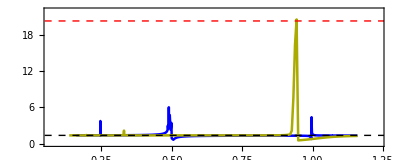

```mathematica
fig4e=Show[ListPlot[{Datafisdis,DatafisdisSigx},Joined->True,
PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{0,22}},GridLines->{{1,1/2,1/3,1/4,1/5,1/6},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.382118818569585,{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],Plot[20.296888693053788,{x,0.0,1.5},PlotStyle->{Dashed,Red,Thick}],AspectRatio->0.4]
```

#### Fig 5 (d)

```mathematica
Datfis={{1.43765,4.932186874422668},{1.4378,2.175427800875245},{1.438,1.9025658993979282},{1.44,1.8509991137529302},{1.8,1.8505934887047815},{2,1.8490726520594976},{2.16,1.8059491659279359},{2.17,2.050910986159062},{2.171,2.4098520132203936},{2.172,3.298437030033955},{2.173,3.5102030571196767},{2.174,3.681261552045513},{2.175,2.935939537410965},{2.176,2.544070205623636},{2.177,2.337317480779564},{2.178,2.217155783271115},{2.179,2.1410414605022092},{2.18,2.089467845215173},{2.19,1.933712460767559},{2.2,1.9017950442484914},{2.3,1.8664960385937475},{2.4,1.8639326692699272},{2.6,1.8646713220813504},{2.8,1.8676055593779266},{3,1.871999643574576},{3.2,1.878121586618649},{3.4,1.8867555776942242},{3.6,1.8995347771044053},{3.8,1.9202005117147356},{4,1.959971455501754},{4.05,1.9769119701239874},{4.1,1.9999844628286758},{4.15,2.0344193373051063},{4.2,2.0963696092899555},{4.21,2.127328073625103},{4.22,2.1428023654901818},{4.23,2.2258853680212685},{4.24,2.2292125002925958},{4.25,2.384247128936587},{4.26,2.7014800928611877},{4.27,2.6301940357461886},{4.28,4.481004478220652},{4.29,3.3962900879621967},{4.3,3.1243651487379553},{4.31,3.4372136653003698},{4.32,4.168709991057375},{4.33,2.8833798300909965},{4.34,2.337359526275622},{4.35,2.402373242787396},{4.36,2.9482683291328056},{4.37,2.4172533463404684},{4.38,1.797095781362147},{4.39,1.2854825556686007},{4.4,1.2790291107257277},{4.45,1.9031033658101442},{4.5,1.4217919139162614},{4.55,0.12656382339696487},{4.6,0.8318712123965564},{4.65,1.2313341847643302},{4.7,1.413129572312737},{4.75,1.5118487473316222},{4.8,1.572901426105342},{4.85,1.614151648240974},{4.9,1.643815149702035},{4.95,1.6661459582907179},{5,1.6835529110212906},{5.1,1.7089162700037872},{5.2,1.7264932163209599},{5.4,1.749228743553875},{5.6,1.7632559885481782},{5.8,1.7727308619806796},{6,1.7795180423735204},{6.2,1.7845704038146801},{6.4,1.7883671496376983},{6.6,1.7918081388142084},{6.8,1.7940368046693607},{7,1.7958874541899517},{7.2,1.7973115329495408},{7.4,1.7983287768372753},{7.6,1.7989186797356767},{7.8,1.7989888866274675},{8,1.798297763901672},{8.2,1.796202996251919},{8.4,1.790550928027511},{8.6,1.768087702369015},{8.65,1.749616564191876},{8.7,1.6703619034380972},{8.75,1.1969655948420455},{8.76,2.4316374200275117},{8.768,1.4557571862502476},{8.77,1.77661022694027},{8.78,1.9826997334002845},{8.79,1.9580578493921093},{8.8,1.933160961063201},{8.85,1.87384880286276},{8.9,1.8528873764038005},{9,1.8361554177700403},{9.2,1.8253609265138622},{9.4,1.8215195685502292},{9.6,1.819692235241883},{10.2,1.8178268669207371}};

DatfisSigx={{1.2,1.827945139961394},{1.3,1.827802582307606},{1.4,1.8276216069451061},{1.5,1.8273943335068448},{1.6,1.8271119924826016},{1.7,1.8268781120714939},{1.72,1.828171032242086},{1.73,3.4903111858310387},{1.74,1.8285047927174645},{1.8,1.8264339519626802},{1.9,1.8258711620519323},{2,1.8252440097283888},{2.1,1.824495604022407},{2.2,1.8235966995301784},{2.3,1.8225139664658339},{2.4,1.8212057853814148},{2.5,1.8196245158650424},{2.6,1.817757264228411},{2.7,1.8159995779082039},{2.8,1.8208206604306054},{2.82,1.8333015937129475},{2.84,1.8477723678785076},{2.86,1.9167271254507803},{2.88,2.2598946748276387},{2.89,2.3801967716945827},{2.9,2.887925994566505},{2.91,2.9539142783483157},{2.92,2.6265638906344115},{2.94,2.0868768417603354},{2.96,1.9499172591265603},{2.98,1.8985845512554491},{3,1.8735104947664758},{3.1,1.8350494852611074},{3.2,1.824263274204354},{3.3,1.8180651914680552},{3.4,1.8131849229878012},{3.5,1.8086952434598556},{3.6,1.8042258869769},{3.7,1.7995909125128047},{3.8,1.794678371118084},{3.9,1.789408940801298},{4,1.783715196769834},{4.1,1.777519883664639},{4.2,1.7706588451853007},{4.3,1.761782106821137},{4.4,1.7588165594446443},{4.5,1.7494299440651495},{4.6,1.740462614784408},{4.7,1.7310803801677161},{4.8,1.7211789514672764},{4.9,1.7107352165771028},{5,1.6997514953785553},{5.1,1.6882443143217316},{5.2,1.6762438086888807},{5.3,1.663780926864092},{5.4,1.6509087466206418},{5.5,1.637681069384823},{5.6,1.6241614634821289},{5.7,1.6104205299032834},{5.8,1.5965346856780718},{5.9,1.582584762286564},{6,1.5686544347924216},{6.1,1.5548285628737375},{6.2,1.5411915133263216},{6.3,1.5278255640592602},{6.4,1.5148094920043849},{6.5,1.5022174567508009},{6.6,1.4901183036568477},{6.7,1.4785754325809004},{6.8,1.4676474240617141},{6.9,1.4573897051106075},{7,1.447857710791884},{7.1,1.439112330577926},{7.2,1.431229073096387},{7.3,1.4243136711829312},{7.4,1.4185295433390985},{7.5,1.4141485304085117},{7.55,1.4126215572700513},{7.6,1.4116508266613237},{7.65,1.4113633560304355},{7.7,1.4119389593626268},{7.75,1.4136383824681353},{7.8,1.4168511635040066},{7.85,1.422181753970906},{7.9,1.430616020543554},{7.95,1.4438753346440851},{8,1.465277415782811},{8.05,1.502310461273775},{8.1,1.5789043940280034},{8.15,3.1913782399485635},{8.2,7.206369005972193},{8.25,7.957423954082055},{8.3,8.31637430174526},{8.35,0.5147310622555332},{8.4,0.5394753718831249},{8.45,0.5654235145148423},{8.5,0.59258062604927},{8.55,0.6209310438424032},{8.6,0.6504329841164482},{8.65,0.6810130430214637},{8.7,0.7125610475271789},{8.75,0.7449260130856711},{8.8,0.7779141669904657},{8.85,0.8112900845760559},{8.9,0.8447818536312358},{8.95,0.8780907415154728},{9,0.9109050806514896},{9.1,0.9738409243829255},{9.2,1.0314814062701023},{9.4,1.1263798592236538},{9.6,1.1944492922427015},{9.8,1.2417495595788275},{10,1.2749867586371242},{10.2,1.2991140132180767}};
```

```mathematica
Datafisher=Table[{Datfis[[i,1]]/(8.801011),Datfis[[i,2]]},{i,1,Length[Datfis]}];
DatafisherSigx=Table[{DatfisSigx[[i,1]]/(8.801011),DatfisSigx[[i,2]]},{i,1,Length[DatfisSigx]}];
```

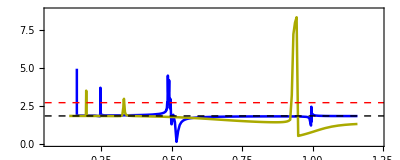

```mathematica
fig4f=Show[ListPlot[{Datafisher,DatafisherSigx},Joined->True,
PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{0,8.75}},GridLines->{{1,1/2,1/3,1/4,1/5,1/6},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.8283437968627987,{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],Plot[2.7,{x,0.0,1.5},PlotStyle->{Dashed,Red,Thick}],AspectRatio->0.4]
```

#### Fig 4 (b)

```mathematica
DatexpH0={{1.43765,-25.096809362395888},{1.4378,-25.14026020121981},{1.438,-25.141641684230756},{1.44,-25.14188085909532},{1.8,-25.141883522963813},{2,-25.141879647993658},{2.16,-25.141620914396537},{2.17,-25.1366035405585},{2.171,-25.12939099875359},{2.172,-25.0846498867483},{2.173,-24.491141088679054},{2.174,-25.111004501750834},{2.175,-25.132752047507697},{2.176,-25.137586157838975},{2.177,-25.13939322619058},{2.178,-25.140259097344032},{2.179,-25.140739701795262},{2.18,-25.141033822493664},{2.19,-25.141727778895554},{2.2,-25.141816049679463},{2.3,-25.141869657793354},{2.4,-25.14186748176166},{2.6,-25.14185639720481},{2.8,-25.14183777658868},{3,-25.14180699459292},{3.2,-25.14175397998379},{3.4,-25.14165637409764},{3.6,-25.14145748486601},{3.8,-25.14098057015407},{4,-25.13944063908771},{4.05,-25.138520440632043},{4.1,-25.137025296989634},{4.15,-25.134358953546304},{4.2,-25.128839252025518},{4.21,-25.126434693630987},{4.22,-25.12474069923317},{4.23,-25.121467327286265},{4.24,-25.118034368942393},{4.25,-25.11176243560136},{4.26,-25.100054036005687},{4.27,-25.09112969689072},{4.28,-24.960611387431708},{4.29,-25.025858119124084},{4.3,-24.976305911563472},{4.31,-24.293588561898172},{4.32,-24.693327693657984},{4.33,-24.81028602458807},{4.34,-24.505602796397497},{4.35,-23.839966562011824},{4.36,-24.52725773857145},{4.37,-24.699380881187693},{4.38,-24.64800209,-24.470908064708887},{4.4,-24.34820022088411},{4.45,-25.0270760062257},{4.5,-25.10410113352826},{4.55,-25.12311632606387},{4.6,-25.130540009949534},{4.65,-25.134206886384483},{4.7,-25.136293703062996},{4.75,-25.137599135705283},{4.8,-25.138472948098567},{4.85,-25.139088352992815},{4.9,-25.139539271955304},{4.95,-25.13988031214168},{5,-25.140145031696434},{5.1,-25.14052463136181},{5.2,-25.140779622363244},{5.4,-25.141092820837823},{5.6,-25.141272492248685},{5.8,-25.141386072881883},{6,-25.141462850277694},{6.2,-25.141517295456136},{6.4,-25.14155725451967},{6.6,-25.141587231053116},{6.8,-25.141610066080514},{7,-25.14162740874672},{7,-25.141640295362787},{7.4,-25.141649235525147},{7.6,-25.141654230435197},{7.8,-25.141654567581202},{8,-25.14164810078335},{8.2,-25.14162871285389},{8.4,-25.14157411622322},{8.6,-25.141319801183577},{8.65,-25.1410582550916},{8.7,-25.140152133220344},{8.75,-25.125386170990296},{8.76,-25.057056168671657},{8.768,-24.768378799780795},{8.77,-24.97348315556851},{8.78,-25.125938568606493},{8.79,-25.13713244079959},{8.8,-25.139850949532427},{8.85,-25.14176317012664},{8.9,-25.141880088110685},{9,-25.141873864159116},{9.2,-25.141834565725507},{9.4,-25.14181477367151},{9.6,-25.141804214434046},{10.2,-25.14179202554895}};
DatexpH0ex={{1.43765,-24.42724599449278},{2.14,-24.426468988635097},{2.15,-24.421040271185326},{2.155,-23.87992529853419},{2.16,-24.41861820696231},{2.17,-24.426351831117906},{2.18,-24.42833760972226},{2.19,-24.427062519175347},{2.2,-24.42712383637883},{2.4,-24.427195243640995},{2.6,-24.427163983994877},{2.8,-24.427110303502825},{3,-24.4270204590584},{3.2,-24.42686359543535},{3.4,-24.42656953015854},{3.6,-24.42595427080364},{3.8,-24.424413379547737},{4,-24.418981570073424},{4.1,-24.409341632147385},{4.15,-24.39720466673523},{4.2,-24.3652752470498},{4.25,-23.789188084433498},{4.3,-23.58661123215887},{4.35,-23.632345201001133},{4.4,-24.225984538642223},{4.5,-24.371217742528636},{4.6,-24.405174010345977},{4.7,-24.41516533756254},{4.8,-24.419453653378397},{4.9,-24.421701934452326},{5,-24.423036534540262},{5.2,-24.424491060578706},{5.6,-24.425672230364377},{6,-24.426144294710053},{6.4,-24.426382456680773},{6.8,-24.42651665400781},{7.2,-24.426593152279274},{7.6,-24.426626123503766},{8,-24.426599582282165},{8.2,-24.42653037431161},{8.4,-24.426311836101704},{8.6,-24.424383416325345},{8.65,-24.418266344473903},{8.66,-24.412888110538436},{8.67,-24.398477496247803},{8.68,-24.33135397754762},{8.69,-23.831973664470212},{8.7,-24.370890253103315},{8.71,-24.41279693938067},{8.72,-24.421522303762256},{8.74,-24.425775609533375},{8.75,-24.426415735041324},{8.76,-24.426763847738655},{8.768,-24.42693211973638},{8.77,-24.426964221105386},{8.78,-24.427083676875245},{8.79,-24.42715613699154},{8.8,-24.427200066458912},{8.85,-24.42724786135372},{8.9,-24.427218914938937},{9,-24.427151259191085},{9.2,-24.427070107401732},{9.4,-24.427030429748708},{9.6,-24.42700884107416},{10.2,-24.426983750620987}};DatexpH0Sigx={{1.2,-25.110989390612197},{1.3,-25.1110836683627},{1.4,-25.111155564781193},{1.5,-25.111210399966247},{1.6,-25.111251743828923},{1.7,-25.11128107624936},{1.72,-25.111276779821225},{1.73,-25.09281623843664},{1.74,-25.111281916633097},{1.8,-25.11130296452808},{1.9,-25.11131596635},{2,-25.111321307197674},{2.1,-25.111319505065232},{2.2,-25.111310644819707},{2.3,-25.11129445660268},{2.4,-25.11127013319794},{2.5,-25.111235696046123},{2.6,-25.111185591096856},{2.7,-25.111098111256414},{2.8,-25.11080454863451},{2.82,-25.110604035668498},{2.84,-25.110219205176897},{2.86,-25.109087179320316},{2.88,-25.104730506283538},{2.9,-25.027148814786923},{2.91,-24.8933095456486},{2.92,-25.090098409770132},{2.94,-25.107445375426664},{2.96,-25.109576526930045},{2.98,-25.110224171049282},{3,-25.110498256034283},{3.1,-25.11078507825069},{3.2,-25.110759995710623},{3.3,-25.1106793057285},{3.4,-25.110572067222527},{3.5,-25.110444284364384},{3.6,-25.110296885765525},{3.7,-25.110129105111067},{3.8,-25.109939383236707},{3.9,-25.10972565531377},{4,-25.109485442585694},{4.1,-25.10921586779313},{4.2,-25.10891362783642},{4.3,-25.108574669361932},{4.4,-25.108195495090182},{4.5,-25.10777092024411},{4.6,-25.107295139815065},{4.7,-25.106762039675576},{4.8,-25.10616444898989},{4.9,-25.10549414355081},{5,-25.10474167620976},{5.1,-25.10389616507239},{5.2,-25.10294503859975},{5.3,-25.101873716020158},{5.4,-25.1006652425884},{5.5,-25.099299811102536},{5.6,-25.09775419582216},{5.7,-25.09600104241323},{5.8,-25.094007984061133},{5.9,-25.091736532013527},{6,-25.089140672702925},{6.1,-25.08616507977816},{6.2,-25.082742815829477},{6.3,-25.078792350757716},{6.4,-25.07421365455653},{6.5,-25.068883020683177},{6.6,-25.06264612440811},{6.7,-25.055308589471},{6.8,-25.046622977120304},{6.9,-25.03627053962545},{7,-25.023835144878674},{7.1,-25.00876520081838},{7.2,-24.99031665034479},{7.3,-24.96746508064613},{7.4,-24.93876536254216},{7.5,-24.902117651472853},{7.6,-24.854355681457672},{7.7,-24.790470036306495},{7.8,-24.701997825298065},{7.9,-24.573199647084323},{8,-24.369802331462665},{8.1,-23.987995554971054},{8.2,-20.761649321273556},{8.3,-16.076572234266724},{8.4,-17.494476929091125},{8.5,-18.82922067901103},{8.6,-19.94116171796335},{8.7,-20.865618658815734},{8.8,-21.630909650476227},{8.9,-22.2603601772601},{9,-22.773899074299486},{9.1,-23.18922359605187},{9.2,-23.52245505961917},{9.4,-23.99980738825961},{9.6,-24.302917472422937},{9.8,-24.499083814305955},{10,-24.630204031207892},{10.2,-24.721064146504524}};
DatexpH0Sigxex={{1.2,-24.3982862876661},{2.86,-24.3689610688457},{2.87,-24.322112832883732},{2.88,-23.819786092754164},{2.89,-24.20628660063636},{2.9,-24.35460241575106},{2.91,-24.379898723968072},{3,-24.397144315460384},{3.4,-24.397803803016657},{3.8,-24.39721555876892},{4.2,-24.39621131361753},{4.6,-24.394603428723777},{5,-24.392036214236764},{5.4,-24.387882787530412},{5.8,-24.380987165739594},{6.2,-24.369068059722142},{6.6,-24.34719008254331},{7,-24.303205962377916},{7.2,-24.263716353435505},{7.3,-24.236094981924253},{7.4,-24.20066281176629},{7.5,-24.15428249397048},{7.6,-24.092009900824248},{7.7,-24.00556946320262},{7.8,-23.879864994736153},{7.9,-23.683376277489323},{8,-23.331446319945247},{8.1,-22.0426537210555},{8.2,-14.593359355812732},{8.3,-15.892079661729502},{8.4,-17.32297799827706},{8.5,-18.65726734533292},{8.6,-19.765027441137942},{8.7,-20.67990306862456},{8.8,-21.42847767618228},{8.9,-22.03278282181962},{9,-22.51260103361183},{9.2,-23.175550858531732},{9.4,-23.564601198164237},{9.6,-23.79545226401876},{9.8,-23.93901742349146},{10,-24.033379497871778},{10.2,-24.098594083765924}};
```

```mathematica
DataexpH0=Table[{DatexpH0[[i,1]]/(8.801011),DatexpH0[[i,2]]/50},{i,1,Length[DatexpH0]}];
DataexpH0ex=Table[{DatexpH0ex[[i,1]]/(8.801011),DatexpH0ex[[i,2]]/50},{i,1,Length[DatexpH0ex]}];
DataexpH0Sigx=Table[{DatexpH0Sigx[[i,1]]/(8.801011),DatexpH0Sigx[[i,2]]/50},{i,1,Length[DatexpH0Sigx]}];
DataexpH0Sigxex=Table[{DatexpH0Sigxex[[i,1]]/(8.801011),DatexpH0Sigxex[[i,2]]/50},{i,1,Length[DatexpH0Sigxex]}];
```

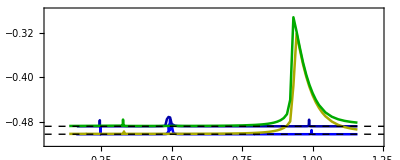

```mathematica
fig4ba=Show[ListPlot[{DataexpH0,DataexpH0ex,DataexpH0Sigx,DataexpH0Sigxex},Joined->True,
PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Blue],Thickness[0.0045]},{Darker[Yellow],Thickness[0.0045]},{Darker[Green],Thickness[0.0045]}},PlotRange->{{0.07,1.23},{-0.52,-0.28}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,LabelStyle->{13,Black}],Plot[{-25.142253953183587/50,-24.42833760972226/50},{x,0.0,1.5},PlotStyle->{{Dashed,Black,Thick},{Dashed,Black,Thick}}],AspectRatio->0.4]
```

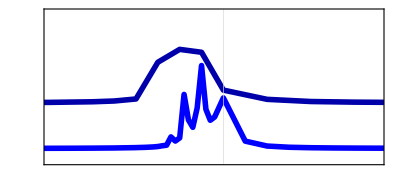

```mathematica
fig4bb=Show[ListPlot[{DataexpH0,DataexpH0ex},Joined->True,
PlotStyle->{{Blue,Thickness[0.01]},{Darker[Blue],Thickness[0.01]},{Darker[Green],Thickness[0.007]}},FrameTicks->None,PlotRange->{{0.455,0.54},{-0.507,-0.46}},GridLines->{{0.5},{}},GridLinesStyle->{{Red,Thickness[0.007],Dashed},{}},Frame->True,LabelStyle->{13,Black}],AspectRatio->0.45]
```

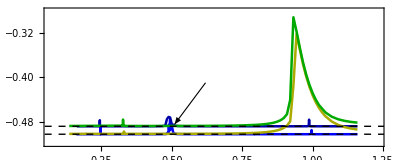
-Graphics-
-Graphics-

```mathematica
fig4g=Show[fig4ba,Graphics@Inset[fig4bb,{0.53,-0.40},{Left,Bottom},Scaled[0.24]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.62,-0.41},{0.51,-0.485}}]}]]
```

#### Fig 4 (a)

```mathematica
DatF1={{1.43765,0.9896893901121767},{1.4378,0.9996200529018111},{1.438,0.9999357904197341},{1.44,0.9999904475225222},{1.8,0.9999895330977169},{2,0.9999871880804628},{2.16,0.9998967431624342},{2.17,0.9981641368400065},{2.171,0.9956735704865795},{2.172,0.9802239208738867},{2.173,0.7752756410673627},{2.174,0.9893241205204745},{2.175,0.9968339422844015},{2.176,0.9985032540197913},{2.177,0.999127268709701},{2.178,0.9994262678725587},{2.179,0.999592225539811},{2.18,0.9996937857393962},{2.19,0.9999333474603569},{2.2,0.9999637428832394},{2.3,0.999981248007366},{2.4,0.999979235057437},{2.6,0.9999718157392854},{2.8,0.9999595564914098},{3,0.9999391522498321},{3.2,0.9999036943515439},{3.4,0.9998378511912095},{3.6,0.9997026717196871},{3.8,0.9993765305198856},{4,0.9983195883166138},{4.05,0.9976882351394726},{4.1,0.9966645677168037},{4.15,0.9948484156642581},{4.2,0.9911403301801764},{4.21,0.9898778573744087},{4.22,0.9884492264995394},{4.23,0.9865424857371834},{4.24,0.9842303199403363},{4.25,0.9808624419985759},{4.26,0.9765272416488741},{4.27,0.9699855948855745},{4.28,0.9356979618866367},{4.29,0.9503608947166396},{4.3,0.9212480350262187},{4.31,0.7163628357960885},{4.32,0.8793680550488481},{4.33,0.8641369968609347},{4.34,0.7222594675929269},{4.35,0.5719089565926511},{4.36,0.8078153959576194},{4.37,0.8388251511888929},{4.38,0.7784703904730617},{4.39,0.6533577253121863},{4.4,0.5090729753510663},{4.45,0.9229450098137715},{4.5,0.9740506644303933},{4.55,0.9869810551560666},{4.6,0.9920833814973701},{4.65,0.9946185641719897},{4.7,0.9960668199823266},{4.75,0.9969752477718361},{4.8,0.9975845843434054},{4.85,0.9980144511884497},{4.9,0.9983298743285188},{4.95,0.9985687351251814},{5,0.9987543502416412},{5.1,0.9990209034669628},{5.2,0.9992002805938938},{5.3,0.9993273818119766},{5.4,0.9994211056202988},{5.6,0.9995481546033073},{5.8,0.9996286879749112},{6,0.9996832711570923},{6.2,0.9997220817438673},{6.4,0.9997506410241775},{6.6,0.9997721733633831},{6.8,0.999788592714859},{7,0.999801125598848},{7.2,0.9998104922965363},{7.4,0.9998170500220395},{7.6,0.999820795143965},{7.8,0.9998212152741482},{8,0.999816775248095},{8.2,0.9998031099700018},{8.4,0.9997643580442837},{8.6,0.9995840726350917},{8.65,0.9993997744111401},{8.7,0.9987785064210728},{8.75,0.9884251454091615},{8.76,0.9407424478279836},{8.768,0.7401553393523722},{8.77,0.8829272560885213},{8.78,0.9889588516387746},{8.79,0.9967219450503717},{8.8,0.9986014030634531},{8.85,0.9999133063233463},{8.9,0.9999897526811296},{9,0.9999819513102106},{9.2,0.9999526636385317},{9.4,0.9999383677169446},{9.6,0.9999308943227435},{10.2,0.9999227576575566}};
DatF3={{1.43765,1.41420333672052*10^-6},{1.4378,1.3350300298389073*10^-6},{1.438,1.3451607057712124*10^-6},{1.44,1.3572099910753032*10^-6},{1.8,3.3381382415179907*10^-6},{2,5.359764409373884*10^-6},{2.16,8.060841168692888*10^-6},{2.17,9.512464183141844*10^-6},{2.171,1.0451785371171067*10^-5},{2.172,1.368818377344753*10^-5},{2.173,3.469839892941838*10^-7},{2.174,4.574651730450348*10^-6},{2.175,6.042047849281713*10^-6},{2.176,6.645949090359748*10^-6},{2.177,6.978868878787963*10^-6},{2.178,7.1932825267928226*10^-6},{2.179,7.345493117822192*10^-6},{2.18,7.4610534229953715*10^-6},{2.19,8.00076713033175*10^-6},{2.2,8.285545409555136*10^-6},{2.3,1.056897077101392*10^-5},{2.4,1.3279314983852472*10^-5},{2.6,2.0929911216329763*10^-5},{2.8,3.322055362280333*10^-5},{3,5.360782165213989*10^-5},{3.2,8.901430064131825*10^-5},{3.4,0.00015475414787405345},{3.6,0.00028970214987471027},{3.8,0.0006151090940714215},{4,0.0016674021014264002},{4.05,0.002294099377238349},{4.1,0.0033069136745774905},{4.15,0.005092690790682448},{4.2,0.008686472857294857},{4.21,0.009839048264658984},{4.22,0.011239580113385363},{4.23,0.012966082292333484},{4.24,0.01511664645820116},{4.25,0.017933167367622935},{4.26,0.021252709037553347},{4.27,0.026651423281744583},{4.28,0.03709989944677973},{4.29,0.03840829283953336},{4.3,0.05875718243197936},{4.31,0.11288430495823641},{4.32,0.033020837163934204},{4.33,0.09292600854835618},{4.34,0.18476138537752837},{4.35,0.06843592675921728},{4.36,5.670146164554855*10^-5},{4.37,0.03467933906524085},{4.38,0.11245810372321238},{4.39,0.23670602845922917},{4.4,0.4323702168373696},{4.45,0.0740408194128825},{4.5,0.02546448328768818},{4.55,0.012871578799858488},{4.6,0.007853171473050228},{4.65,0.005347059745939597},{4.7,0.003911164721158761},{4.75,0.003008777744215613},{4.8,0.0024027061165668257},{4.85,0.001974743446091294},{4.9,0.0016604988347890981},{4.95,0.0014224029715026554},{5,0.0012373039844996736},{5.1,0.000971367839926927},{5.2,0.0007923201092456885},{5.3,0.000665408309055599},{5.4,0.0005717996152453495},{5.6,0.0004448711980559351},{5.8,0.0003643912717409454},{6,0.00030983314818078516},{6.2,0.00027103499727789527},{6.4,0.00024248751437734906},{6.6,0.00022091976146801741},{6.8,0.0002045132865466007},{7,0.00019197908741798675},{7.2,0.00018260889613393186},{7.4,0.00017604685319602372},{7.6,0.00017229708879395604},{7.8,0.0001718722677274811},{8,0.00017630769530745195},{8.2,0.0001899681132020914},{8.4,0.00022871003459251461},{8.6,0.0004088340745607748},{8.65,0.0005924638313348188},{8.7,0.0011976240620605483},{8.75,0.01156952418207588},{8.76,0.059253577070594685},{8.768,0.25982128271648863},{8.77,0.11705572534321772},{8.78,0.011031573213471826},{8.79,0.0032696816226177737},{8.8,0.0013906890703056706},{8.85,7.940645251273118*10^-5},{8.9,3.100885757829489*10^-6},{9,1.0991065952966946*10^-5},{9.2,4.0320778754704914*10^-5},{9.4,5.4625219618021434*10^-5},{9.6,6.209879747114854*10^-5}};
DatF5={{1.43765,2.3225297929974996*10^-7},{1.4378,2.447496721083398*10^-10},{1.438,3.761517187908834*10^-9},{1.44,7.492751534407777*10^-9},{1.8,6.001741483153633*10^-8},{2,3.826027999117827*10^-7},{2.16,8.805563111317178*10^-5},{2.17,0.0018186089450039644},{2.171,0.004307433207927819},{2.172,0.01974905988444434},{2.173,0.22465145154777258},{2.174,0.01066135710996681},{2.175,0.0031521616892005314},{2.176,0.001482691059130755},{2.177,0.0008585024617724545},{2.178,0.0005593616351733124},{2.179,0.0003932902576202969},{2.18,0.0002916369248877334},{2.19,5.1579414881649125*10^-5},{2.2,2.0901309071651504*10^-5},{2.3,1.1063040739897207*10^-6},{2.4,4.0265286288422963*10^-7},{2.6,1.5565132221971722*10^-7},{2.8,1.0248860574951947*10^-7},{3,8.949980003538008*10^-8},{3.2,9.913307104370012*10^-8},{3.4,1.4192503179858004*10^-7},{3.6,2.7984281900512884*10^-7},{3.8,8.520368104503413*10^-7},{4,5.1421786073412515*10^-6},{4.05,9.612404462000129*10^-6},{4.1,2.014053336969419*10^-5},{4.15,4.9667799870734755*10^-5},{4.2,0.0001590677476134063},{4.21,0.00020993321124009875},{4.22,0.0002861527250972273},{4.23,0.0004043471459392848},{4.24,0.0005780340760628797},{4.25,0.0009151215654854631},{4.26,0.001163706246510048},{4.27,0.0024466172683292823},{4.28,0.00917313588003482},{4.29,0.0025147992411110077},{4.3,0.012643551391242399},{4.31,0.09209659046873427},{4.32,0.01239476884508969},{4.33,0.00138202034221273},{4.34,0.032437492625413275},{4.35,0.25805507328236865},{4.36,0.15498066211375328},{4.37,0.10939948668103207},{4.38,0.09823735359060026},{4.39,0.10150157618303576},{4.4,0.055753587047436014},{4.45,0.0029462157149492386},{4.5,0.00047459002848520545},{4.5,0.00014115661195226176},{4.6,5.765662348845641*10^-5},{4.65,2.8542316441932606*10^-5},{4.7,1.607459976647212*10^-5},{4.75,9.93071939442783*10^-6},{4.8,6.577434745850139*10^-6},{4.85,4.599263796919433*10^-6},{4.9,3.3586958234075278*10^-6},{4.95,2.541326716914468*10^-6},{5,1.9804344560786425*10^-6},{5.1,1.2911567014322923*10^-6},{5.2,9.061465771355322*10^-7},{5.3,6.725681820669749*10^-7},{5.4,5.21500014935309*10^-7},{5.6,3.4576909778747834*10^-7},{5.8,2.517622947521255*10^-7},{6,1.9538043858911636*10^-7},{6.2,1.5786262060430318*10^-7},{6.4,1.2539761232039838*10^-7},{6.6,1.4343170276121378*10^-7},{6.8,1.156844803987374*10^-7},{7,1.0418751143807025*10^-7},{7.2,9.664983367868561*10^-8},{7.4,9.162496134210473*10^-8},{7.6,8.872625419191606*10^-8},{7.8,8.812224968550631*10^-8},{8,9.079304562334736*10^-8},{8.2,1.0000506295208923*10^-7},{8.4,1.301249914312807*10^-7},{8.6,3.8195990973048365*10^-7},{8.65,.127700584439899*10^-6},{8.7,1.7403885992303933*10^-5},{8.75,4.108236868388365*10^-8},{8.76,1.5058926337268865*10^-8},{8.768,9.276706846163585*10^-7},{8.77,5.493600454811352*10^-7},{8.78,1.198012452246278*10^-7},{8.79,5.355429644905914*10^-8},{8.8,2.804031767415668*10^-8},{8.85,4.864085472790662*10^-10},{8.9,1.6664781208176824*10^-9},{9,1.01618964032814*10^-8},{9.2,2.1381464173185925*10^-8},{9.4,2.688297236285814*10^-8},{9.6,2.981849888531349*10^-8}};
DatF1Sigx={{1.2,0.9993641524333439},{1.3,0.9993603817064933},{1.4,0.9993546240981761},{1.5,0.9993467050099879},{1.6,0.9993363778143941},{1.7,0.9993230774682326},{1.72,0.9993175828950014},{1.73,0.9942265655611018},{1.74,0.9993146550943827},{1.8,0.9993072390105996},{1.9,0.9992877537214023},{2,0.9992642880579938},{2.1,0.9992363370170732},{2.2,0.9992032671656151},{2.3,0.9991643056900533},{2.4,0.9991184355589139},{2.5,0.9990640874009851},{2.6,0.9989980171290368},{2.7,0.998909489276208},{2.8,0.9987199432705821},{2.82,0.9986201813791068},{2.84,0.9984308050333003},{2.86,0.9979233678489382},{2.88,0.9962021685670172},{2.9,0.9603130011961304},{2.91,0.8984652441847489},{2.92,0.9890864603463998},{2.94,0.9970775603174061},{2.96,0.9980490475075832},{2.98,0.9983347025405799},{3,0.9984472420088308},{3.1,0.9985029329207702},{3.2,0.998404329259683},{3.3,0.9982689842343586},{3.4,0.9981090731609765},{3.5,0.9979259409511264},{3.6,0.9977184193128096},{3.7,0.9974843741369928},{3.8,0.9972211002113363},{3.9,0.9969254270631169},{4,0.996593729841843},{4.1,0.9962218994475358},{4.2,0.995805284226438},{4.3,0.9953384536101425},{4.4,0.9948162556600052},{4.5,0.9942310878793699},{4.6,0.993575679119018},{4.7,0.9928413992141227},{4.8,0.9920184083554753},{4.9,0.9910954758499213},{5,0.9900597496308507},{5.1,0.9888964822766492},{5.2,0.9875887031596191},{5.3,0.9861168271026902},{5.4,0.9844581770721883},{5.5,0.9825864139072735},{5.6,0.9804708373083577},{5.7,0.9780755343937747},{5.8,0.9753583345055162},{5.9,0.9722695203113774},{6,0.9687502302559213},{6.1,0.9647304679558057},{6.2,0.9601266082578755},{6.3,0.9548382550855806},{6.4,0.9487442597658996},{6.5,0.9416976459829979},{6.6,0.9335191030679403},{6.7,0.9239885953111221},{6.8,0.9128344814325896},{6.9,0.8997193331530321},{7,0.8842213720316934},{7.1,0.8658101002163391},{7.2,0.8438142908652676},{7.3,0.817380083896834},{7.4,0.7854166858139369},{7.5,0.7465275973147033},{7.6,0.6989276494910337},{7.7,0.6403534857921301},{7.8,0.5679946809871108},{7.9,0.4785197264562118},{8,0.36836095058341745},{8.1,0.234237060197332},{8.2,0.057634071870658776},{8.25,0.02848579630312},{8.3,0.018394342898438433},{8.4,0.000368617057173273},{8.5,1.113798265677704*10^-6},{8.6,2.2709850538849653*10^-5},{8.7,0.00024094625433651243},{8.8,0.0015104149363453553},{8.9,0.006218562128287944},{9,0.01836887414459847},{9.1,0.04189685512840789},{9.2,0.07836875158031058},{9.4,0.18153039598862378},{9.6,0.29876489435993203},{9.8,0.4066487373913875},{10,0.49676241918129294},{10.2,0.5691760812600468}};
```

```mathematica
DataF1=Table[{DatF1[[i,1]]/(8.801011),DatF1[[i,2]]},{i,1,Length[DatF1]}];
DataF3=Table[{DatF3[[i,1]]/(8.801011),DatF3[[i,2]]},{i,1,Length[DatF3]}];
DataF5=Table[{DatF5[[i,1]]/(8.801011),DatF5[[i,2]]},{i,1,Length[DatF5]}];
DataF1Sigx=Table[{DatF1Sigx[[i,1]]/(8.801011),DatF1Sigx[[i,2]]},{i,1,Length[DatF1Sigx]}];
```

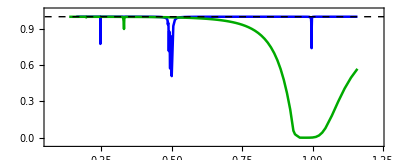

```mathematica
fig4h=Show[ListPlot[{DataF1,DataF1Sigx},Joined->True,PlotRange->{{0.07,1.23},{-0.05,1.05}},GridLines->{{1/6,1/5,1/4,1/3,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.002],Dashed},{}},Frame->True,PlotStyle->{{Blue,Thickness[0.0045]},{Darker[Green],Thickness[0.0045]}},PlotLegends->{},LabelStyle->{14,Black}],Plot[1,{x,0.0,1.5},PlotStyle->{Dashed,Black,Thick}],AspectRatio->0.4]
```